```mathematica
X2000={{1,0.2207537588},{2,0.4836899469},{3,0.5360044102},{4,0.6033635813},{5,0.6218350336},{6,0.6562103372},{7,0.6664624606},{8,0.6878925885},{9,0.6947839725},{10,0.7102965671},{11,0.7155156259},{12,0.7267360208},{13,0.7309462467},{14,0.7395440184},{15,0.7429752122},{16,0.7498090143},{17,0.7525560937},{18,0.7575158217},{19,0.7595240856},{20,0.7628062504},{21,0.7640349054},{22,0.7660690350},{23,0.7667983894},{24,0.7677499340},{25,0.7680083397},{26,0.7679592099},{27,0.7677998140},{28,0.7667971042},{29,0.7661803962},{30,0.7641678589},{31,0.7630342259},{32,0.7598761615},{33,0.7582282886},{34,0.7537433101},{35,0.7513726341},{36,0.7449926618},{37,0.7416573451},{38,0.7330150624},{39,0.7284021355},{40,0.7164930986},{41,0.7099174787},{42,0.6930445405},{43,0.6832131653},{44,0.6583152221},{45,0.6421446539},{46,0.6013235188},{47,0.5677530371},{48,0.4800536964},{49,0.3640482214}};
```

```mathematica
X=X10000={{1,0.4805852554},{2,0.5394177945},{3,0.6526652630},{4,0.6714438491},{5,0.7309904479},{6,0.7408498209},{7,0.7803768028},{8,0.7868413824},{9,0.8154212040},{10,0.8200119371},{11,0.8415062482},{12,0.8449165162},{13,0.8614610704},{14,0.8640724059},{15,0.8767778336},{16,0.8787444708},{17,0.8884272940},{18,0.8899492050},{19,0.8972089204},{20,0.8983648184},{21,0.9031912677},{22,0.9038464381},{23,0.9062311788},{24,0.9065115421},{25,0.9067277682},{26,0.9067054382},{27,0.9047030522},{28,0.9042251898},{29,0.8998274977},{30,0.8988717603},{31,0.8920002419},{32,0.8905546368},{33,0.8812204154},{34,0.8793234179},{35,0.8671709885},{36,0.8646323768},{37,0.8487681250},{38,0.8454538190},{39,0.8247256507},{40,0.8203646282},{41,0.7927937919},{42,0.7868888626},{43,0.7489783382},{44,0.7407083227},{45,0.6850829258},{46,0.6720091749},{47,0.5723983575},{48,0.5402831196},{49,0.1622957665}};
```

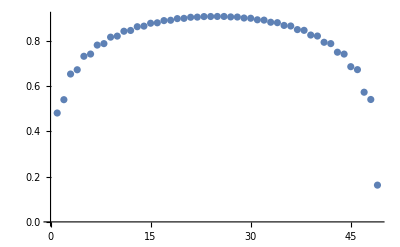

```mathematica
ListPlot[X]
```

```mathematica
XX=Select[X,#⟦1⟧> 10 && #⟦1⟧<40 &];
```

```mathematica
model= c/3 Log[Sin[Pi x/50]]+d;
```

```mathematica
fit=FindFit[XX,model,{c,d},x]
```

{c→0.489597,d→0.906719}

```mathematica
modelf=Function[{x},Evaluate[model/.fit]];
```

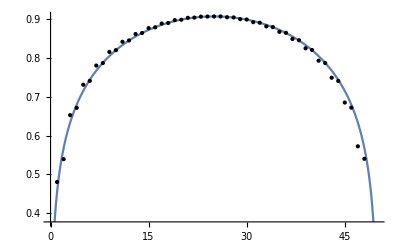

```mathematica
Plot[modelf[x],{x,0,50},Epilog->Map[Point,X]]
```